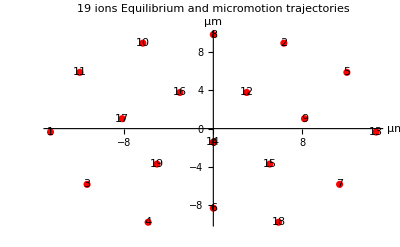

```mathematica
Subscript[w, x]=2*2 Pi 0.18*10^6;
Subscript[w, y]=2*2 Pi 0.22*10^6;
Subscript[w, z]=2*2.21*2Pi*10^6;
K=8.987551*10^9*(1.602*10^-19)^2;
n1= 3;
n=3 n1^2-3 n1+1;
M=171*1.66*10^-27;
g=0.01 M Subscript[w, x];
(*Setting the equilibrium positions with NNS*)
d= 10* 10^-6;
(*Psuedopotential with strong supression in z direction*)

V1[t_]:=1/2 M∑_(i=1)^n (Subscript[w, x]^2(Subscript[x, i][t])^2+Subscript[w, y]^2(Subscript[y, i][t])^2)
(*Coulomb interaction with strong supression in z direction*)
V2[t_]:=∑_(j=1)^n ∑_(i=j+1)^n K((Subscript[y, i][t]-Subscript[y, j][t])^2+(Subscript[x, i][t]-Subscript[x, j][t])^2)^(-1/2)
V3[t_]:=V1[t]+V2[t]
V4[t_]:=Flatten[Table[{-D[V3[t],Subscript[x, i][t]],-D[V3[t],Subscript[y, i][t]]},{i,n}]]
V5[t_]:=Flatten[Table[{-g Subscript[x, i]'[t],-g Subscript[y, i]'[t]},{i,n}]]
V6[t_]:=Flatten[Table[{M Subscript[x, i]''[t],M Subscript[y, i]''[t]},{i,n}]]
a1:=Flatten[Table[{x0,0},{x0,-(n1-1)d,(n1-1)d,d}]]
a2:=Flatten[Table[Flatten[Table[{x0+d/2 l2,d/2 l2 √3},{x0,-(n1-1)d,(n1-1-l2)d,d}]],{l2,1,n1-1}]]
a3:=Flatten[Table[Flatten[Table[{x0+d/2 l2,-(d/2 l2 √3)},{x0,-(n1-1)d,(n1-1-l2)d,d}]],{l2,1,n1-1}]]
a4:=a1~Join~a2~Join~a3
E1:=a4~Join~Table[0,{i,2n}]

E2:=Flatten[Table[{Subscript[x, i][0],Subscript[y, i][0]},{i,n}]]~Join~Flatten[Table[{Subscript[x, i]'[0],Subscript[y, i]'[0]},{i,n}]]
sol=NDSolve[{V6[t]==V4[t]+V5[t], E2==E1},Flatten[Table[{Subscript[x, i],Subscript[y, i]},{i,n}]],{t,0,2000/Subscript[w, x]},Method->{"EquationSimplification"->"Residual"},MaxSteps->Infinity];
p2=ListPlot[10^6 Table[{Subscript[x,i][2000/Subscript[w,x]],Subscript[y,i][2000/Subscript[w,x]]},{i,n}]/. sol,PlotStyle->Red,PlotLabel->"19 ions Equilibrium and micromotion trajectories",AxesLabel->{"μm","μm"},Epilog->Table[Text[i,Flatten[10^6 {Subscript[x,i][2000/Subscript[w,x]],Subscript[y,i][2000/Subscript[w,x]]}/. sol,1],{1.2,0}],{i,n}]]
```

```mathematica
(*Until now, we are solving the equilibrium positions by psuedopotential. Here we solve the problem by Mathieu equations.*)
V7[t_]:=∑_(j=1)^n ∑_(i=j+1)^n K((Subscript[y, i][t]-Subscript[y, j][t])^2+(Subscript[x, i][t]-Subscript[x, j][t])^2)^(-1/2)
(*in-plane Mathieu equation: d^2/dt^2 Subscript[n, n]*)
(*Calculate full potential -Graphics-*)
(*Coulomb interaction derivative*)
V13[t_]:=Table[D[V7[t],Subscript[x, i][t]],{i,n}];
V14[t_]:=Table[D[V13[t],Subscript[x, j][t]],{j,n}];
V15=V14[2000/Subscript[w, x]] /.sol;
MC=V15//.{x_List}:>x;
(*Coulomb interaction derivative*)
V24[t_]:=Table[D[V7[t],Subscript[y, i][t]],{i,n}];
V25[t_]:=Table[D[V24[t],Subscript[y, j][t]],{j,n}];
V26=V25[2000/Subscript[w, x]] /.sol;
MC2=V26//.{x_List}:>x;
(*Coulomb interaction derivative*)
V27[t_]:=Table[D[V7[t],Subscript[x, i][t]],{i,n}];
V28[t_]:=Table[D[V27[t],Subscript[y, j][t]],{j,n}];
V29=V28[2000/Subscript[w, x]] /.sol;
MC3=V29//.{x_List}:>x;
(*Coulomb interaction derivative*)
V30[t_]:=Table[D[V7[t],Subscript[y, i][t]],{i,n}];
V31[t_]:=Table[D[V30[t],Subscript[x, j][t]],{j,n}];
V32=V31[2000/Subscript[w, x]] /.sol;
MC4=V32//.{x_List}:>x;
m1={{1,0},{0,0}};
m2={{0,0},{0,1}};
m3={{0,1},{0,0}};
m4={{0,0},{1,0}};
MC11=KroneckerProduct[m1,MC];
MC22=KroneckerProduct[m2,MC2];
MC33=KroneckerProduct[m3,MC3];
MC44=KroneckerProduct[m4,MC4];
MC55=MC11+MC22+MC33+MC44;
e=1.602*10^-19;
U1=1*-1.1;
r=0.01;
d1=200*10^-6;
2(1+r)e U1/(d1)^2;
MDC1= {{2(1+r)e U1/(d1)^2,0},{0,0}};
V5=IdentityMatrix[n];
MDC2=KroneckerProduct[MDC1,V5];
MDC3= {{0,0},{0,2(1-r)e U1/(d1)^2}};
MDC4=KroneckerProduct[MDC3,V5];
MDC5=MDC4+MDC2;(*MDC5 is -Graphics-*)
MCD=MC55+MDC5;
(*Calculate g=Subscript[m, c]-Subscript[M, c] r^(0)*)(*-Graphics--Graphics-*)

V13[t_]:=Table[{D[V7[t],Subscript[x, i][t]]},{i,n}];
mc=V13[2000/Subscript[w, x]] /.sol;
V13[t_]:=Table[{D[V7[t],Subscript[y, i][t]]},{i,n}];
mc1=V13[2000/Subscript[w, x]] /.sol;
mc2=mc[[1]]~Join~mc1[[1]];
R01=Table[{Subscript[x, i][2000/Subscript[w, x]]},{i,n}]/.sol;
R02=Table[{Subscript[y, i][2000/Subscript[w, x]]},{i,n}]/.sol;
R011=R01[[1]];
R022=R02[[1]];
R03=R011~Join~R022;
(*equilibrium positions of x and y*)
g1=mc2-MC55.R03;
g2=Flatten[g1];

(*g2 is -Graphics-*)

(*Calculate RF potential-Graphics- *)
Ω=1*2π*50*10^6;
V0=1*90;
d0=200*10^(-6);
VR[b_]:=DiagonalMatrix[Flatten[Table[e V0*Cos[2*b]/(d0)^2,{i,1,2n}]]];
(*finding transformation Q such that -Graphics-*)
Q1=Transpose[Normalize/@Eigenvectors[MCD]];
MCDQ=Inverse[Q1].MCD.Q1;
(*Q1 is the transformation*)
(*We list out our decoupled Mathieu equations*)
(*Here I will try the fourth method from paper*)
(*-Graphics-*)
(*We have equations: Subscript[s, i]''[b]+(4(MCDQ+2 VR[b]))/(M Ω^2).s2[b]= -4/(M Ω^2)(Q1.g2)*)
(*Compared with the method above: Subscript[f, 0]=-4/(M Ω^2)(Inverse[Q1].g2),a=(4MCDQ)/(M Ω^2)], q=-(4 VR[b])/(M Ω^2 Cos[2b]), Here, Subscript[f, 0] are column matrices and so does a and q determined by the mode numbers which is 2 times the ions number, 2n. *)
Clear[b]
(*Compute above Matrix*)
Table[Subscript[IDD, i]=(-4( VR[b]))/(M Ω^2 Cos[2b])/((4MCDQ)/(M Ω^2)-4 i^2),{i,1,5}];
Table[{mi=Table[0,{i,1,5},{i,1,5}],mi[[1+q ]][[1+q ]]=1,Subscript[w, q+1]=mi},{q,0,4}];
Table[{ti=Table[0,{i,1,5},{i,1,5}],ti[[2+q ]][[1+q ]]=1,Subscript[t, q+1]=ti},{q,0,3}];
Table[{vi=Table[0,{i,1,5},{i,1,5}],vi[[1+q ]][[2+q ]]=1,Subscript[v, q+1]=vi},{q,0,3}];
Subscript[am, 1]=KroneckerProduct[Subscript[w, 1],(4MCDQ)/(M Ω^2)];
Subscript[am, 2]=KroneckerProduct[Subscript[v, 1],(4( VR[b]))/(M Ω^2 Cos[2b])];
Subscript[am, 3]=KroneckerProduct[Subscript[t, 1],-2 Subscript[IDD, 1]];
Subscript[am, 4]=KroneckerProduct[Subscript[w, 2],IdentityMatrix[2n]];
Subscript[am, 5]=KroneckerProduct[Subscript[v, 2],-Subscript[IDD, 1]];
Subscript[am, 6]=KroneckerProduct[Subscript[t, 2],-Subscript[IDD, 2]];
Subscript[am, 7]=KroneckerProduct[Subscript[w, 3],IdentityMatrix[2n]];
Subscript[am, 8]=KroneckerProduct[Subscript[v, 3],-Subscript[IDD, 2]];
Subscript[am, 9]=KroneckerProduct[Subscript[t, 3],-Subscript[IDD, 3]];
Subscript[am, 10]=KroneckerProduct[Subscript[w, 4],IdentityMatrix[2n]];
Subscript[am, 11]=KroneckerProduct[Subscript[v, 4],-Subscript[IDD, 3]];
Subscript[am, 12]=KroneckerProduct[Subscript[t, 4],-Subscript[IDD, 4]];
Subscript[am, 13]=KroneckerProduct[Subscript[w, 5],IdentityMatrix[2n]];
Vam=Table[Subscript[am, i],{i,1,13}];
amm=Sum[Vam[[i]],{i,1,13}];
c1=Table[{1},{i,1,2n}]~Join~Table[{0},{i,1,8n}];
cc1=Inverse[amm].c1;
cc2=Table[cc1[[i]],{i,1,2n}];
Mf=DiagonalMatrix[Table[-4/(M Ω^2)(Inverse[Q1].g2)[[i]],{i,1,2n}]];
Mf.cc2;
rc0=Q1.Mf.cc2;
(*first order micromotion*)
c13=Table[cc1[[i]],{i,2n+1,4n}];
Mf.c13;(*micromotion asscociated with each mode*)
rc1=Q1.Mf.c13;
rc1//MatrixForm;(*10^-6~10^-7m*)
(*Second order micromotion*)
c14=Table[cc1[[i]],{i,4n+1,6n}];
Mf.c14;
rc2=Q1.Mf.c14;
rc2//MatrixForm;(*10^-9~10^-10m*)
(*Third order micromotion*)
c15=Table[cc1[[i]],{i,6n+1,8n}];
Mf.c15;
rc3=Q1.Mf.c15;
rc3//MatrixForm;
(*10^-12~10^-13m*)
rc00=Flatten[rc0];
rc11[b_]:=Flatten[rc1 Cos[2 b]];
rc22[b_]:=Flatten[rc2 Cos[4 b]];
rc33[b_]:=Flatten[rc3 Cos[6 b]];
rr[b_]:=rc00+rc11[b]+rc22[b]+rc33[b]
aa=Flatten[Table[Subscript[x, i][2000/Subscript[w, x]]/.sol,{i,1,n}]~Join~Table[Subscript[y, i][2000/Subscript[w, x]]/.sol,{i,1,n}]];
1/n Sum[(((aa-rc00)[[i]])^2+((aa-rc00)[[i+n]])^2)^(1/2),{i,1,n}];
p4=ListPlot[Table[{rr[b][[i]],rr[b][[i+n]]},{i,1,n},{b,0,2π,π/100}],PlotStyle->Brown];
(*Show[p3,p4]*)
p3=Manipulate[ListPlot[10^6 Table[{rr[b][[i]],rr[b][[i+n]]},{i,1,n}],PlotStyle->Red,PlotRange->{{-20,20},{-15,15}},AxesLabel->{"m","m"},PlotLabel->"Micromotion trajectories"],{b,0,2 π}]
aa=Flatten[Table[Subscript[x, i][2000/Subscript[w, x]]/.sol,{i,1,n}]~Join~Table[Subscript[y, i][2000/Subscript[w, x]]/.sol,{i,1,n}]];
rc00=Flatten[rc0];
1/n Sum[(((aa-rc00)[[i]])^2+((aa-rc00)[[i+n]])^2)^(1/2),{i,1,n}];(*mean deviations of two methods*)
Vz7[t_]:=∑_(j=1)^n ∑_(i=j+1)^n K((Subscript[y, i][t]-Subscript[y, j][t])^2+(Subscript[x, i][t]-Subscript[x, j][t])^2+(Subscript[z, i][t]-Subscript[z, j][t])^2)^(-1/2)
(*Coulomb interaction derivative*)
Vz13[t_]:=Table[D[Vz7[t],Subscript[z, i][t]],{i,n}];
Vz14[t_]:=Table[D[Vz13[t],Subscript[z, j][t]],{j,n}];
q=-0.051;
q=-0.051;
Vz15=Vz14[2000/Subscript[w, x]](1+ 3/4 q^2)/.sol;
Vz16=Vz15//.{x_List}:>x
Vz17=Vz16/.Table[Subscript[z, i][2000/Subscript[w, x]]->0,{i,1,n}];
VzD=DiagonalMatrix[Table[M Subscript[w, z]^2,{i,1,n}]];
VVZ=VzD+Vz17;
(1/M Eigenvalues[VVZ])^(1/2);
Subscript[w, p/z]=1/Subscript[w, z](1/M Eigenvalues[VVZ])^(1/2);
```